```mathematica
SetDirectory[NotebookDirectory[]];
nff[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)-μ)/T]+1);
nfa[mf2_,q_,T_,μ_]:=1/(Exp[(√(q^2+mf2)+μ)/T]+1);
nfd1xf[mf2_,q_,T_,μ_]:=(nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.))/T;
nfd2xf[mf2_,q_,T_,μ_]:=1/T^2 nff[mf2,q,T,μ](nff[mf2,q,T,μ]-1.)(2.*nff[mf2,q,T,μ]-1.);
nfd1xa[mf2_,q_,T_,μ_]:=(nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.))/T;
nfd2xa[mf2_,q_,T_,μ_]:=1/T^2 nfa[mf2,q,T,μ](nfa[mf2,q,T,μ]-1.)(2.*nfa[mf2,q,T,μ]-1.);
nb[Epi_,T_]:=1/(Exp[Epi/T]-1);
nbd1x[Epi_,T_]:=-1/T nb[Epi,T](nb[Epi,T]+1);
mf2[h_,ρ_]:=(h^2 ρ)/2;
Eq[q_,mf2_]:=√(q^2+mf2);
Epi[q_,mp2_]:=√(q^2+mp2);
Nf=2;
Nc=3;
h=6.5;
λ=20.;
ν=-490.^2;
c=1.7*10^-3*(10^3)^3;
μ=0.;
M1=700;
F1B2thr[mp2_,mf2_,p0_,q_,T_,mu_]:=1/2 (-(0+nb[Epi[q,mp2],T])/(2 Epi[q,mp2]^3 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))+nbd1x[Epi[q,mp2],T]/(2 Epi[q,mp2]^2 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))-nb[Epi[q,mp2],T]/(2 Epi[q,mp2]^3 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2))+nbd1x[Epi[q,mp2],T]/(2 Epi[q,mp2]^2 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2))-nfa[mf2,q,T,mu]/(Eq[q,mf2] (-Epi[q,mp2]^2+(-Eq[q,mf2]-mu+ⅈ p0)^2)^2)-(-0+nff[mf2,q,T,mu])/(Eq[q,mf2] (-Epi[q,mp2]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)^2)+((0+nb[Epi[q,mp2],T]) (-Epi[q,mp2]-mu+ⅈ p0))/(Epi[q,mp2]^2 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2)^2)-(nb[Epi[q,mp2],T] (Epi[q,mp2]-mu+ⅈ p0))/(Epi[q,mp2]^2 (-Eq[q,mf2]^2+(Epi[q,mp2]-mu+ⅈ p0)^2)^2));
F1B2vac[mp2_,mf2_,p0_,q_,T_,mu_]:=1/2 (-1/(2 Epi[q,mp2]^3 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2))--1/(Eq[q,mf2] (-Epi[q,mp2]^2+(Eq[q,mf2]-mu+ⅈ p0)^2)^2)+((1) (-Epi[q,mp2]-mu+ⅈ p0))/(Epi[q,mp2]^2 (-Eq[q,mf2]^2+(-Epi[q,mp2]-mu+ⅈ p0)^2)^2));
Zpsi[mp2_,mf2_,h_,p0_,T_,mu_,Λvac_]:=(Nf^2-1)/(2Nf)*h^2/(3 π^2)(NIntegrate[q^4 Re[F1B2thr[mp2,mf2,p0,q,T,mu]],{q,1,100,200,300,400,500,1000,2000,3000}]+NIntegrate[q^4 Re[F1B2vac[mp2,mf2,p0,q,T,mu]],{q,1,Λvac}])+1
```

```mathematica
fpidata=Transpose[Import["../../../../sigma0.dat"]];
mu=Flatten[Table[i*5.,{i,1,80,1}]];
T=Table[i,{i,10,250,20}];
```

```mathematica
T1=10;
mpi=Flatten[Table[√(Flatten[Import["../../input/T"<>ToString[T1]<>"/sigma"<>ToString[i]<>".dat"]][[1]]),{i,5,400,5}]];
datav1000=Table[Zpsi[mpi[[i]]^2,mf2[6.5,(fpidata[[T1]][[i]])^2/2],6.5,π  T1,T1,mu[[i]],1000.],{i,1,80}];
(*datav2000=Table[Zpsi[mpi[[i]]^2,mf2[6.5,(fpidata[[T1]][[i]])^2/2],6.5,π  T1,T1,mu[[i]],2000.],{i,1,80}];
datav3000=Table[Zpsi[mpi[[i]]^2,mf2[6.5,(fpidata[[T1]][[i]])^2/2],6.5,π  T1,T1,mu[[i]],3000.],{i,1,80}];*)
Export["./T"<>ToString[T1]<>"/Zpsi.dat",Re[datav1000]]
```

./T10/Zpsi.dat

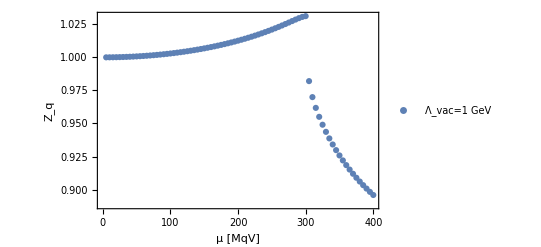

```mathematica
ListPlot[{Transpose[{mu,datav1000/datav1000[[1]]}](*,Transpose[{mu,datav2000/datav2000[[1]]}],Transpose[{mu,datav3000/datav3000[[1]]}]*)},Frame->True,FrameLabel->{"μ [MqV]","Z_q"},PlotLegends->{"Λ_vac=1 GeV","Λ_vac=2 GeV","Λ_vac=3 GeV"}]
```

```mathematica
T1=50;
mpi=Flatten[Table[√(Flatten[Import["../../input/T"<>ToString[T1]<>"/sigma"<>ToString[i]<>".dat"]][[1]]),{i,5,400,5}]];
datav1000=Table[Zpsi[mpi[[i]]^2,mf2[6.5,(fpidata[[T1]][[i]])^2/2],6.5,π  T1,T1,mu[[i]],1000.],{i,1,80}];
Export["./T"<>ToString[T1]<>"/Zpsi.dat",Re[datav1000]]
```

./T50/Zpsi.dat

```mathematica
T1=190;
mpi=Flatten[Table[√(Flatten[Import["../../input/T"<>ToString[T1]<>"/sigma"<>ToString[i]<>".dat"]][[1]]),{i,5,400,5}]];
datav1000=Table[Zpsi[mpi[[i]]^2,mf2[6.5,(fpidata[[T1]][[i]])^2/2],6.5,π  T1,T1,mu[[i]],1000.],{i,1,80}];
Export["./T"<>ToString[T1]<>"/Zpsi.dat",Re[datav1000]]
```

./T190/Zpsi.dat